```mathematica
vmax=2;
p=0.1;
rho=Round[(1-p)/(vmax+1-2*p),0.001];
dmin=Round[rho*0.3,0.001];
dmax=Round[rho*1.5,0.001];
dd=Round[(dmax-dmin)/12,0.001];
rho " :Transition density!!!"
dmin ": Min density"
dmax ": Max density"
dd ": density step"
"List of simulated values:"
For[i=-1,i<12,i++;
Print[dmin+i*dd]
]
```

0.321  :Transition density!!!

0.096 : Min density

0.482 : Max density

0.032 : density step

List of simulated values:

0.096

0.128

0.16

0.192

0.224

0.256

0.288

0.32

0.352

0.384

0.416

0.448

0.48

0.1

16384. = L

5767 = N

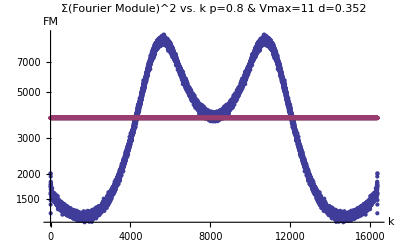

3737.3 = N*(L-N)/(L-1)

4781.34 = Mean of o.7 largest values

6.12282×10^7 = Sum of All L-1 Valus

6.12282×10^7 = N*(L-N)

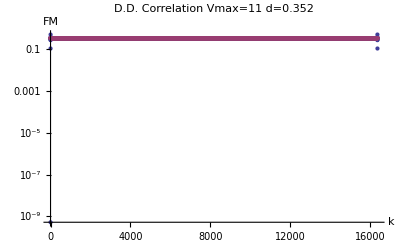

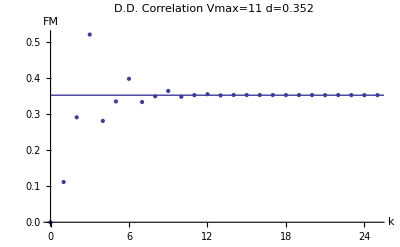

0.35195 = (N-1)/(L-1)

0.352031 = Mean of o.9 largest values

0.35195 = Mean of all L-1 values

0.00345765 = STDV of all L-1 values

0.00982425 = STDV/Mean

5766. = Sum of All L Valus

5766 = N-1

Values lesser than 2/3*(N-1)/(L-1):

{0,5.29176×10^-10}

{1,0.111537}

```mathematica
d="0.352";
p="0.1"
n=16384.000;
a="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax2/short/fourier.1d.averaged.d";
b=".p"<>p<>".v2.txt";
g=".p"<>p<>".v2.txt";
c=a<>d<>b;
e="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax2/short/ddensitycorrelation.d";
f=e<>d<>g;
j=StringToStream[d];
o= Read[j,Number];
m=Floor[o*16384];
n "= L"
m  "= N  "
bitF=ReadList[c,{Number,Number}];
bitf2=bitF[[All,2]];
randomf=Table[{i,(n-m)*m/(n-1)},{i,0,16383}];
ListLogPlot[{bitF,randomf},PlotLabel->"Σ(Fourier Module)^2 vs. k  p=0.8 & Vmax=11 d="<>  d,AxesLabel->{k,FM},PlotRange->Full]
(n-m)*m/(n-1) "= N*(L-N)/(L-1)"
TrimmedMean[bitf2,{0.3,0}] "= Mean of o.7 largest values"
summ=Sum[bitf2[[i]],{i,1,n-1} ];
N[summ] "= Sum of All L-1 Valus"
m*(n-m) "= N*(L-N)"
Δ=summ-m*(n-m);
density=ReadList[f,{Number,Number}];
density2=density[[All,2]];
prand=(m-1)/(n-1);
random=Table[{i,prand},{i,0,16383}];
ListLogPlot[{density,random},PlotLabel->"D.D. Correlation Vmax=11 d="<>  d,AxesLabel->{k,FM},PlotRange->Full]
pic1=ListPlot[density,PlotLabel->"D.D. Correlation Vmax=11 d="<>  d,AxesLabel->{k,FM},PlotRange->{{0,25},Full}];
pic2=ListLinePlot[random];
Show[pic1,pic2]
prand  "= (N-1)/(L-1)"
TrimmedMean[density2,{0.1,0}] "= Mean of o.9 largest values"
mean=Mean[Delete[density2,1]] "= Mean of all L-1 values"
stdv=StandardDeviation[Delete[density2,1]]  "= STDV of all L-1 values"
StandardDeviation[Delete[density2,1]]/Mean[Delete[density2,1]] "= STDV/Mean"
summ2=Sum[density2[[i]],{i,1,n} ];
N[summ2] "= Sum of All L Valus"
m2=m-1;  
m2 "= N-1"
"Values lesser than 2/3*(N-1)/(L-1):"
For[i=0,i<50,i++,
If[density2[[i]]<2*prand/3,
Print[{i-1,density2[[i]]}]
]
]
```